```mathematica
ClearAll["Global`*"]
```

# Template 2

## , , ,

## Case

```mathematica
(* Given parameter *)
beta=1;
v = 1;
```

```mathematica
g1[tau_]:=Piecewise[{{1,0<tau<1/beta}},0];
L[tau_] := v/beta*g1[tau];
f[tau_,q_]:=L[tau]*√(v/beta) √((1 + ((q*L[tau])/3)^2)/(1 + ((q*L[tau])/2)^2 +((q*L[tau])/3)^6)) ;
```

## Fourier transform ,

```mathematica
fTdf[q0_?NumericQ,q_?NumericQ]:=NIntegrate[f[tau,q]*Exp[-I*q0*tau],{tau,0,1/beta}];
fstarTdf[q0_?NumericQ,q_?NumericQ]:=NIntegrate[ComplexExpand[f[tau,q]]*Exp[I*q0*tau],{tau,0,1/beta}];
DeltaS[q0_?NumericQ,q_?NumericQ]:=fTdf[q0,q]*fstarTdf[q0,q];
spectrumFixedRatio[q0_?NumericQ,r_?NumericQ]:=q0^3 DeltaS[q0,q0/r];
```

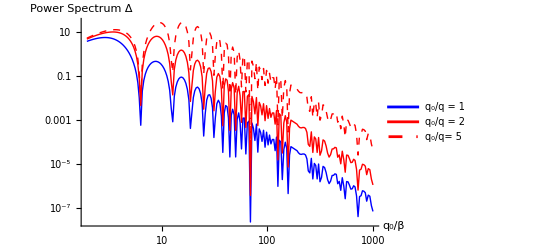

```mathematica
LogLogPlot[{spectrumFixedRatio[q0,1.0],spectrumFixedRatio[q0,2.0],spectrumFixedRatio[q0,5.0]},{q0,0.0,1000.0},AxesLabel->{"q_0/β","Power Spectrum Δ"},PlotLegends->{"q_0/q = 1","q_0/q = 2","q_0/q= 5"},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Red,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Varying velocity and PT time scale

```mathematica
ClearAll["Global`*"]
```

```mathematica
g1[tau_,beta_]:=Piecewise[{{1,0<tau<1/beta}},0];
L[tau_,beta_,v_] := v/beta*g1[tau,beta];
f[tau_,q_,beta_,v_]:=L[tau,beta,v]*√(v/beta) √((1 + ((q*L[tau,beta,v])/3)^2)/(1 + ((q*L[tau,beta,v])/2)^2 +((q*L[tau,beta,v])/3)^6)) ;
fTdf[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=NIntegrate[f[tau,q,beta,v]*Exp[-I*q0*tau],{tau,0,1/beta}];
fstarTdf[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=NIntegrate[ComplexExpand[f[tau,q,beta,v]]*Exp[I*q0*tau],{tau,0,1/beta}];
DeltaS[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=fTdf[q0,q,beta,v]*fstarTdf[q0,q,beta,v];
spectrum[q0_?NumericQ,r_?NumericQ,beta_?NumericQ,v_?NumericQ]:=q0^3 DeltaS[q0,q0/r,beta,v];
```

## Velocity

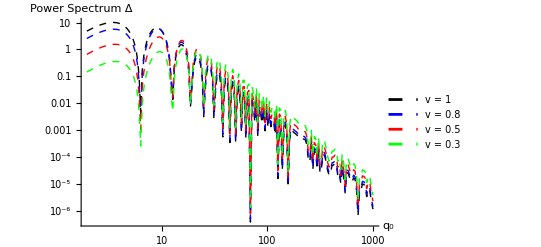

```mathematica
LogLogPlot[{spectrum[q0,2.0,1,1],spectrum[q0,2.0,1,0.8],spectrum[q0,2.0,1,0.5],spectrum[q0,2.0,1,0.3]},{q0,0.0,1000.0},AxesLabel->{"q_0","Power Spectrum Δ"},PlotLegends->{"v = 1","v = 0.8","v = 0.5","v = 0.3"},PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Blue,Dashed],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Inverse time PT

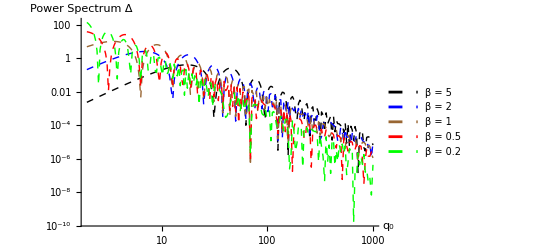

```mathematica
LogLogPlot[{spectrum[q0,2.0,5,1],spectrum[q0,2.0,2,1],spectrum[q0,2.0,1,1],spectrum[q0,2.0,0.5,1],spectrum[q0,2.0,0.2,1]},{q0,0.0,1000.0},AxesLabel->{"q_0","Power Spectrum Δ"},PlotLegends->{"β = 5","β = 2","β = 1","β = 0.5","β = 0.2"},PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Blue,Dashed],Directive[Thick,Brown,Dashed],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Final abundance , where ,

```mathematica
G = 1;
h = 0.67;
ρc = (3 *h^2)/(8 π G);
```

```mathematica
fh[q0_,q_]:=((q0^2-q^2)^2)/2;
cJ = 4/3;(* scalar*)
diffΩIntegrand[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=fh[q0,q]/q*DeltaS[q0,q,beta,v];
diffΩ[q0_?NumericQ,beta_?NumericQ,v_?NumericQ]:=2 cJ/(320 π^2)*NIntegrate[diffΩIntegrand[q0,q,beta,v],{q,10^-5,q0}];
Ω[beta_?NumericQ,v_?NumericQ]:=NIntegrate[diffΩ[q0,beta,v],{q0,0,2*beta},Method->"GlobalAdaptive"];
```

```mathematica
(* consider ultrarelativistic bubbles *)
βvalues = {0.2,0.5,1,2,5};
Ωvalues = ConstantArray[0,Length[βvalues]];
For[i=1,i<=Length[βvalues],i++,Ωvalues[[i]]=Ω[βvalues[[i]],1]];
```

```mathematica
dataΩβ = Transpose[{βvalues,Ωvalues}];
```

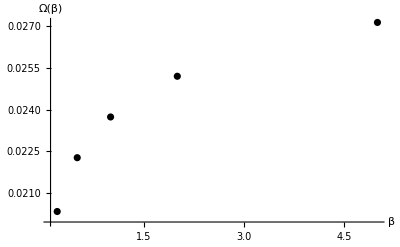

```mathematica
ListPlot[dataΩβ,AxesLabel->{"β","Ω(β)"},PlotStyle->{Directive[Black]},PlotRange->All]
```

## Case

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Given parameter *)
beta=1;
v = 1;
```

```mathematica
g2[tau_]:=Piecewise[{{4*beta^2 tau *(1/beta-tau),0<tau<1/beta}},0];
L[tau_] := v/beta*g2[tau];
f[tau_,q_]:=L[tau]*√(v/beta) √((1 + ((q*L[tau])/3)^2)/(1 + ((q*L[tau])/2)^2 +((q*L[tau])/3)^6)) ;
fTdf[q0_?NumericQ,q_?NumericQ]:=NIntegrate[f[tau,q]*Exp[-I*q0*tau],{tau,0,1/beta}];
fstarTdf[q0_?NumericQ,q_?NumericQ]:=NIntegrate[ComplexExpand[f[tau,q]]*Exp[I*q0*tau],{tau,0,1/beta}];
DeltaS[q0_?NumericQ,q_?NumericQ]:=fTdf[q0,q]*fstarTdf[q0,q];
spectrumFixedRatio[q0_?NumericQ,r_?NumericQ]:=q0^3 DeltaS[q0,q0/r];
```

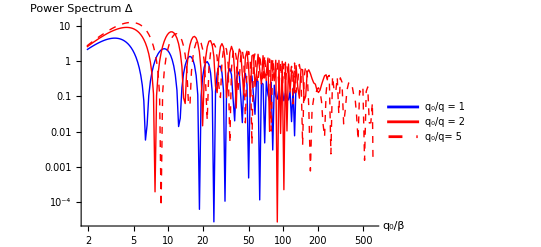

```mathematica
LogLogPlot[{spectrumFixedRatio[q0,1.0],spectrumFixedRatio[q0,2.0],spectrumFixedRatio[q0,5.0]},{q0,0.0,1000.0},AxesLabel->{"q_0/β","Power Spectrum Δ"},PlotLegends->{"q_0/q = 1","q_0/q = 2","q_0/q= 5"},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Red,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Varying velocity and PT time scale

```mathematica
ClearAll["Global`*"]
```

```mathematica
g2[tau_,beta_]:=Piecewise[{{4*beta^2 tau *(1/beta-tau),0<tau<1/beta}},0];
L[tau_,beta_,v_] := v/beta*g2[tau,beta];
f[tau_,q_,beta_,v_]:=L[tau,beta,v]*√(v/beta) √((1 + ((q*L[tau,beta,v])/3)^2)/(1 + ((q*L[tau,beta,v])/2)^2 +((q*L[tau,beta,v])/3)^6)) ;
fTdf[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=NIntegrate[f[tau,q,beta,v]*Exp[-I*q0*tau],{tau,0,1/beta}];
fstarTdf[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=NIntegrate[ComplexExpand[f[tau,q,beta,v]]*Exp[I*q0*tau],{tau,0,1/beta}];
DeltaS[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=fTdf[q0,q,beta,v]*fstarTdf[q0,q,beta,v];
spectrum[q0_?NumericQ,r_?NumericQ,beta_?NumericQ,v_?NumericQ]:=q0^3 DeltaS[q0,q0/r,beta,v];
```

## Velocity

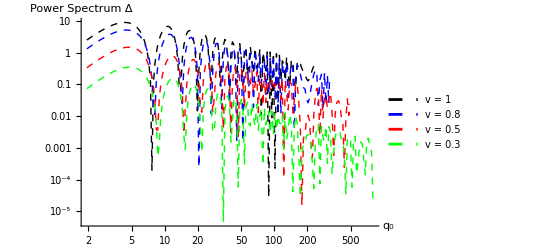

```mathematica
LogLogPlot[{spectrum[q0,2.0,1,1],spectrum[q0,2.0,1,0.8],spectrum[q0,2.0,1,0.5],spectrum[q0,2.0,1,0.3]},{q0,0.0,1000.0},AxesLabel->{"q_0","Power Spectrum Δ"},PlotLegends->{"v = 1","v = 0.8","v = 0.5","v = 0.3"},PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Blue,Dashed],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Inverse time PT

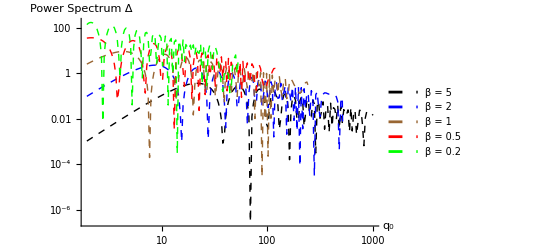

```mathematica
LogLogPlot[{spectrum[q0,2.0,5,1],spectrum[q0,2.0,2,1],spectrum[q0,2.0,1,1],spectrum[q0,2.0,0.5,1],spectrum[q0,2.0,0.2,1]},{q0,0.0,1000.0},AxesLabel->{"q_0","Power Spectrum Δ"},PlotLegends->{"β = 5","β = 2","β = 1","β = 0.5","β = 0.2"},PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Blue,Dashed],Directive[Thick,Brown,Dashed],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Final abundance

```mathematica
G = 1;
h = 0.67;
ρc = (3 *h^2)/(8 π G);
```

```mathematica
fh[q0_,q_]:=((q0^2-q^2)^2)/2;
cJ = 4/3;(* scalar*)
diffΩIntegrand[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=fh[q0,q]/q*DeltaS[q0,q,beta,v];
diffΩ[q0_?NumericQ,beta_?NumericQ,v_?NumericQ]:=2 cJ/(320 π^2)*NIntegrate[diffΩIntegrand[q0,q,beta,v],{q,10^-5,q0}];
Ω[beta_?NumericQ,v_?NumericQ]:=NIntegrate[diffΩ[q0,beta,v],{q0,0,2*beta},Method->"GlobalAdaptive"];
```

```mathematica
(* consider ultrarelativistic bubbles *)
βvalues = {0.2,0.5,1,2,5};
Ωvalues = ConstantArray[0,Length[βvalues]];
For[i=1,i<=Length[βvalues],i++,Ωvalues[[i]]=Ω[βvalues[[i]],1]];
```

```mathematica
dataΩβ = Transpose[{βvalues,Ωvalues}];
```

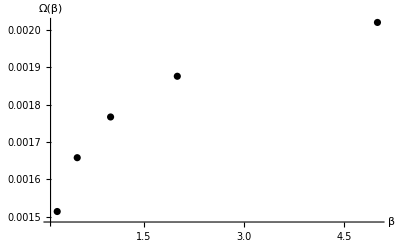

```mathematica
ListPlot[dataΩβ,AxesLabel->{"β","Ω(β)"},PlotStyle->{Directive[Black]},PlotRange->All]
```